## Modelo de Drude

```mathematica
ℏ=6.582119569*10^(-16)
```

6.58212×10^-16

```mathematica
ϵ[ℏω_,ωp_,γ_]:=Module[{ω=ℏω/ℏ},1-(ωp^2/(ω(ω+I γ)))]
```

```mathematica
ωp1=4.3/ℏ;
ωp2=10/ℏ;
γ1=0.15/ℏ;
```

```mathematica
ϵ[ωp1,ωp1,γ1]
```

1.+9.94764×10^-48 ⅈ

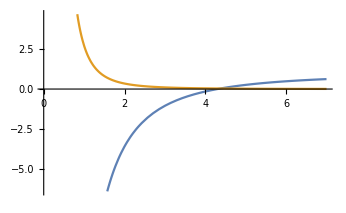

```mathematica
Plot[{Re[ϵ[ℏω,ωp1,γ1]],Im[ϵ[ℏω,ωp1,γ1]]},{ℏω,0,7}]
```

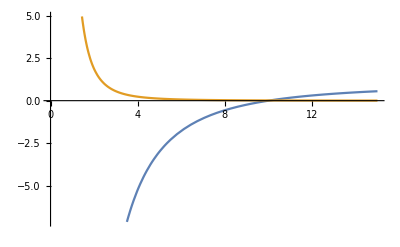

```mathematica
Plot[{Re[ϵ[ℏω,ωp2,γ1]],Im[ϵ[ℏω,ωp2,γ1]]},{ℏω,0,15}]
```

## Cálculo de las secciones transversales de absorción, esparcimiento y extinción

Definiendo los factores de depolarización para un elipsoide

```mathematica
f[q_,a_,b_,c_]:=Sqrt[(a^2+q)(b^2+q)(c^2+q)]
```

```mathematica
l[j_,a_,b_,c_]:=Module[{n= a b c *0.5},
				Which[j==1,n*NIntegrate[1/((a^2+q) (f[q,a,b,c])),{q,0,Infinity}],
					j==2,n*NIntegrate[1/((b^2+q) (f[q,a,b,c])),{q,0,Infinity}],
					j==3,n*NIntegrate[1/((c^2+q) (f[q,a,b,c])),{q,0,Infinity}]]]
```

```mathematica
(*************************************************************************************************************)
(*Pruebas *)
```

```mathematica
Timing[l[1,1,1,1]]
```

{0.015625,0.333333}

```mathematica
(*************************************************************************************************************)
```

Redefiniendo los factores de depolarización considerando los casos para un elipsoide oblato (a=b) L1= L2 y uno prolato (b=c) L2=L3

```mathematica
elipsoblato[j_,a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2)},Which[j==1|| j==2,(gac/(2 (eac2))) (π/2-ArcTan[gac])-((gac)^2)/2,
						j==3,(a^2 c)/2* NIntegrate[1/((c^2+q) (f[q,a,b,c])),{q,0,Infinity}]]]
```

```mathematica
elipsprolato[j_,a_,b_,c_]:=Module[{eab2=1-(b^2/a^2)},Which[j==1,((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]),
						j==2||j==3,(a^2 b)/2 *NIntegrate[1/((b^2+q) (f[q,a,b,c])),{q,0,Infinity}]]]
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[j,a,b,c],
							b==c ,elipsprolato[j,a,b,c],True,l[j,a,b,c]]
```

```mathematica
Timing[l[2,2,3,2]]
```

{0.015625,0.232981}

```mathematica
Timing[factgeom[2,2,3,2]]
```

{0.,0.232981}

Definiendo las polarizabilidades en cada dirección, considerando ϵ1 la permitividad eléctrica en el interior del elipsoide y ϵm la permitividad eléctrica al exterior de este

```mathematica
α[j_,a_,b_,c_,ϵ1_,ϵm_]:=4 π a b c ((ϵ1-ϵm)/ (3 ϵm + 3 factgeom[j,a,b,c] (ϵ1-ϵm)))
```

Definiendo las secciones transversales de extinción, absorción y esparcimiento

```mathematica
k[λ_]:=2 π/λ
```

```mathematica
Cext[j_,λ_,a_,b_,c_,ℏω_,ωp1_,γ1_,ϵm_]:=Module[{ϵ1=1-(ωp1^2/((ℏω/ℏ)((ℏω/ℏ)+I γ1)))},
														k[λ] Im[4 π a b c ((ϵ1-ϵm)/ (3 ϵm + 3 factgeom[j,a,b,c] (ϵ1-ϵm)))]]
```

```mathematica
Cscat[j_,λ_,a_,b_,c_,ℏω_,ωp1_,γ1_,ϵm_]:=(Norm[4 π a b c ((ϵ1-ϵm)/ (3 ϵm + 3 factgeom[j,a,b,c] (ϵ1-ϵm)))]^2 k[λ]^4)/6 π
```

```mathematica
Cabs[j_,λ_,a_,b_,c_,ℏω_,ωp1_,γ1_,ϵm_]:=Cext[j,λ,a,b,c,ℏω,ωp1,γ1,ϵm]-Cscat[j,λ,a,b,c,ℏω,ωp1,γ1,ϵm]
```